```mathematica
Manipulate[
z =0.5r ⅇ^(ⅈ ϕ);
zConj = Conjugate[z];
zcSum = z + zConj;

g1 = Graphics[{
Circle[{0, 0}, r],
Dashed,
Line[{{0,0}, {Re[z], Im[z]}}],
Gray,
Line[{{0,0}, {Re[z], -Im[z]}}],
Dashing[None],
Black,
Line[{{0, 0}, {Re[zcSum], Im[zcSum]}}],
Red,
PointSize[Large],
Point[{Re[z], Im[z]}],
Green,
Point[{Re[z], -Im[z]}]
}, PlotRange->{{ -2, 2}, {-2, 2}}, Axes->True];
p1 = ParametricPlot[Evaluate[Dot[RotationMatrix[-90 Degree],{x,r Cos[2π x - ϕ]}]],{x,0,2}, Axes->False];

Show[g1,p1],
{ϕ, -2 π, 2 π},
{ϕ, {0, π/2, π, (3π)/2, 2π}},
{r, 0.5, 2}, {r, {0.5, 1, 1.5, 2}}]
```

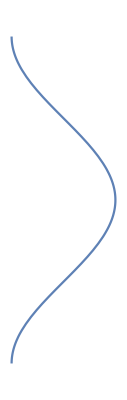

```mathematica
ParametricPlot[Evaluate[Dot[RotationMatrix[90 Degree],{x,Cos[x]}]],{x,0,2}, Axes->False]
```